```mathematica
K2meV=0.08617332;
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Defect_annealed/NEB"];
neb4850=ReadList["NEB_4850",{Number,Number,Number,Number,Number}];
eform=ReadList["SP_SPperf_diff",{Number,Number,Number,Number}];
neb4850//TableForm;
ListPlot@Transpose@{Transpose[neb4850][[2]],Transpose[neb4850][[3]]};
dataplot=ListPlot[Transpose@{Transpose[neb4850][[1]],Transpose[neb4850][[3]]}];
Plot[Interpolation[Transpose@{Transpose[neb4850][[1]],Transpose[neb4850][[3]]},InterpolationOrder->2][x],{x,0,9}];
Plot[BezierFunction[Transpose@{Transpose[neb4850][[1]],Transpose[neb4850][[3]]}][x],{x,0,9}];
```

4.625 | -671.501 | -675.312 | -3.81121
4.6583 | -672.026 | -675.603 | -3.57701
4.685 | -672.04 | -675.424 | -3.38458
4.691 | -671.994 | -675.335 | -3.34034
4.73 | -671.297 | -674.347 | -3.05035
4.759 | -670.344 | -673.171 | -2.82737
4.801 | -668.355 | -670.847 | -2.49198
4.85 | -665.205 | -667.241 | -2.03622

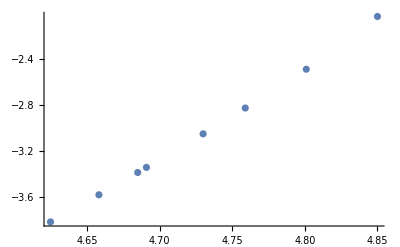

```mathematica
eform//TableForm
ListPlot@Transpose@{Transpose[eform][[1]],Transpose[eform][[4]]}
```

```mathematica
Join[Transpose[neb4850][[1]],{8.5}]
Transpose[neb4850][[1]]
Join[Transpose[neb4850][[3]],-1.4]
```

{0,1,2,3,4,5,6,7,8,9,8.5}

{0,1,2,3,4,5,6,7,8,9}

Apply[0.001+Join[{0.,0.009433,0.046668,0.383155,0.310989,0.896086,0.985949,1.09269,-1.25224,-2.07754},-1.4]]

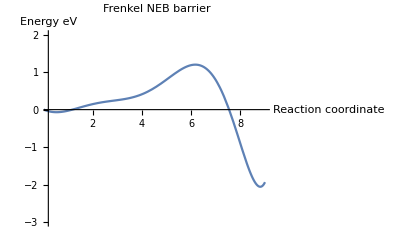

```mathematica
fitt[x_]:=Fit[Transpose@{Join[Transpose[neb4850][[1]],{8.7}],Join[Transpose[neb4850][[3]],{-1.7}]},{1,x,x^2,x^3,x^4,x^5,x^6,x^7},x]
fitplot=Plot[Evaluate@fitt[x],{x,0,9},PlotRange->{{0.2,9},{-3,2}},PlotLabel->"Frenkel NEB barrier",AxesLabel->{"Reaction \n coordinate","Energy\n eV"},Ticks->None]
```

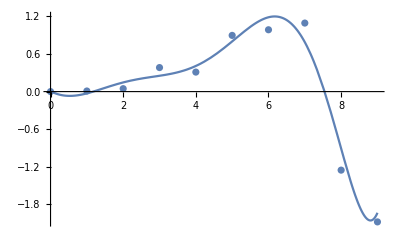

```mathematica
Show[fitplot,dataplot]
```

```mathematica
Plot[fitt[x],{x,1,10}]
```

General::ivar: 1.00018 is not a valid variable.

General::ivar: 1.18386 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Transpose[neb4850][[3]]
```

{0.,0.009433,0.046668,0.383155,0.310989,0.896086,0.985949,1.09269,-1.25224,-2.07754}

```mathematica
listplot3d={{0,0,0},{4,0,0},{8,0,0},{0,8,0},{4,8,2},{8,8,4}}
```

{{0,0,0},{4,0,0},{8,0,0},{0,8,0},{4,8,2},{8,8,4}}

```mathematica
ListPlot3D[listplot3d,InterpolationOrder->10,PlotRange->All]
```

-Graphics3D-

-∞

```mathematica
Log[2]//N
```

0.693147

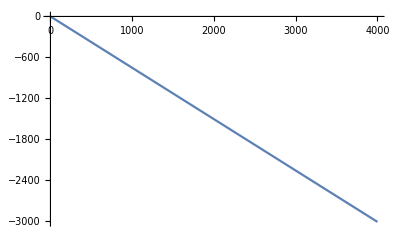

```mathematica
(*Frenkel entropy contribution *)
Plot[-K2meV*(Log[32]+Log[192])*T,{T,1,4000}]
```